```mathematica
dtot=100000
dw = 50000
B=1.5*10^-14
v=32.3
E0=-(dtot*B*v)/(dw*4)
e=1.60217646*10^-19
m=9.10938188*10^-31
```

100000

50000

1.5×10^-14

32.3

-2.4225×10^-13

1.60218×10^-19

9.10938×10^-31

```mathematica
32.3
```

32.3

```mathematica
β=(e (4 E0^2+B E0 v))/(4 (m v^3))
```

1.53148×10^-19

```mathematica
A=-e*β/m
```

-2.6936×10^-8

```mathematica
Bz[y_]=E0/(v+(B/4+E0/v)*e*y/m)
```

-(2.4225×10^-13)/(32.3-0.000659558 y)

{{y→InterpolatingFunction[{{0.,1548.}},<>],x→InterpolatingFunction[{{0.,1548.}},<>]}}

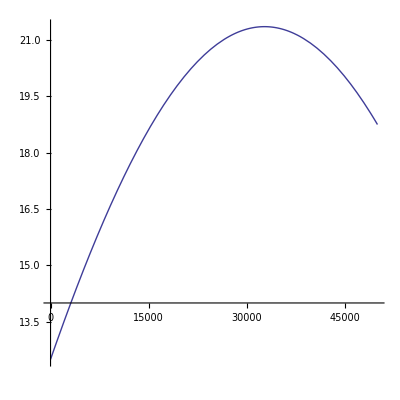

```mathematica
t=.
sol=NDSolve[{y''[t]==((-x'[t]*Bz[y[t]])+E0)*e/m,y'[0]==32.3*Sin[.0005],y[0]==25000Sin[.0005],x''[t]==e/m*(Bz[y[t]])*y'[t],x[0]==0*25000,x'[0]==32.283511},{y,x},{t,0,1548}]
ParametricPlot[{x[t],y[t]}/.sol,{t,0,1548},AspectRatio-> 1]
```

```mathematica
{x[t],y[t]}/.sol
```

{{InterpolatingFunction[{{0.,1548.}},<>][t],InterpolatingFunction[{{0.,1548.}},<>][t]}}

```mathematica
x[t]/.sol
```

{InterpolatingFunction[{{0.,1548.}},<>][t]}

```mathematica
s=OpenWrite[FileNameJoin[{NotebookDirectory[],"mathematica.dat"}]]
For[i=0,i<=1548,i=i+20,Write[s,(x[i] /. sol)[[1]]+25000 ,a , 4*m*v/(e*B)+(y[i] /. sol)[[1]]]]
Close[s]
```

OutputStream[D:\Research\2011-Fall\mathematica.dat,34]

D:\Research\2011-Fall\mathematica.dat

```mathematica
{(x[33] /. sol)[[1]] , (y[33] /. sol)[[1]]}
```

```mathematica
a=" "
```